```mathematica
data={{0,0.45/0.45 210},{0.001,0.454577/0.45 210},{0.002,0.459081/0.45 210},{0.005,0.472155/0.45 210},{0.01 ,0.492564/0.45 210},{0.02,0.528701/0.45 210},{0.03,0.559411/0.45 210},{0.04,0.585539/0.45 210},{0.05,0.607799/0.45 210},{0.06,0.626794/0.45 210},{0.07,0.643032/0.45 210},{0.08,0.656942/0.45 210},{0.09,0.668887/0.45 210},{0.10 ,0.679172/0.45 210},{0.12 ,0.695760/0.45 210},{0.14 ,0.708326/0.45 210},{0.16 ,0.718025/0.45 210},{0.20 ,0.731879/0.45 210},{0.25 ,0.743463/0.45 210},{0.3 ,0.752122/0.45 210},{0.5 ,0.779564/0.45 210},{1.0 ,0.84424/0.45 210},{11.0 ,2.13664/0.45 210}};
PLFUN[epbar_,data_]:=Block[{y,y0,m,x,x0,val,X,vecfunc,i,list,vec,sigmay,media,H},
val=0;
list=data;
For[i=1,i< Length[list],i++,
If[Between[epbar,{list[[i,1]],list[[i+1,1]]}],

x0=list[[i,1]];
y0=list[[i,2]];
x=list[[i+1,1]];
y=list[[i+1,2]];
m=(y-y0)/(x-x0);
media=(list[[i,2]]+list[[i+1,2]])/2;
sigmay=m(epbar-x0)+y0;
H=m;
Return[{sigmay,H}];

];
];

];
```

```mathematica
FromTensorToVec[tensor_]:={tensor[[1,1]],tensor[[2,2]],tensor[[1,2]]}
FromVecToTensor[vec_]:={{vec[[1]],vec[[3]]},{vec[[3]],vec[[2]]}}
```

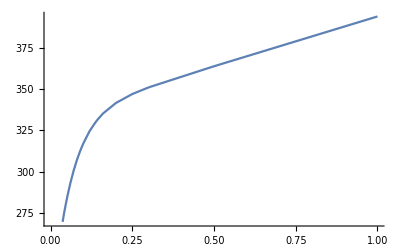

```mathematica
Plot[PLFUN[ep,data][[1]],{ep,0,1}]
```

```mathematica
ApplyStrainComputeStress1[etrial_,epsp_,sigmay_,young_,nu_,epbarn_]:=Block[{q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS},

G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));

trialstrain=(etrial-epsp);
hardeningvariable=epbarn;

P=K (trialstrain[[1]]+trialstrain[[2]]);

S=2 G(trialstrain-(1/3(trialstrain[[1]]+trialstrain[[2]]){1,1,0}));

trialstress=S+P{1,1,0};


trSS=S[[1]]^2  + S[[2]]^2 + 2 S[[3]]^2 ;
q=Sqrt[3/2 (trSS)];
Print["antes =",q];
q=√((1-nu+nu^2) trialstress[[1]]^2+3 trialstress[[3]]^2+(-1-2 nu+2 nu^2) trialstress[[1]] trialstress[[2]]+(1-nu+nu^2) trialstress[[2]]^2);
Print["depois =",q];
qtr=q;
Str=S;
phi=q- sigmay;

If[phi≥ 0,
gamma=(q-sigmay)/(3G +H);
S*=(1-((gamma 3 G)/q));
updatedstrain=S/(2G)+1/3 (trialstrain[[1]]+trialstrain[[2]]){1,1,0};
hardeningvariable=gamma;
updatedstress=S+P {1,1,0};
(*Print["qint = ",q];*)
Dep=ComputeDep[young,nu,{Str,P,qtr},gamma];
,
updatedstrain=trialstrain;
updatedstress=S+P{1,1,0};
Dep=ComputeDep[young,nu,{Str,P,qtr},0];
];



(*Print["S = ",S];
Print["{sigx-P,sigy-P,sigxy} = ",{updatedstress[[1,1]]-P,updatedstress[[2,2]]-P,updatedstress[[1,2]]}];*)
{updatedstrain,updatedstress,hardeningvariable,Dep}

]
```

```mathematica
Clear[nu]
sig={{sigxx,sigxy,0},{sigxy,sigyy,0},{0,0,nu(sigxx+sigyy)}};
(*sig={{sigxx,sigxy},{sigxy,sigyy}};*)
S=sig-1/3 Tr[sig]IdentityMatrix[3]//Simplify
q=Sqrt[3/2 Tr[S.S]]//Simplify//Simplify
phi=q- 3 G dgamma-sigyy;
n={D[phi,sigxx],D[phi,sigyy],D[phi,sigxy]}//Simplify
FromVecToTensor[n];
```

{{1/3 (2 sigxx-sigyy-nu (sigxx+sigyy)),sigxy,0},{sigxy,1/3 (-sigxx+2 sigyy-nu (sigxx+sigyy)),0},{0,0,1/3 (-1+2 nu) (sigxx+sigyy)}}

√((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)

{(2 (1-nu+nu^2) sigxx+(-1-2 nu+2 nu^2) sigyy)/(2 √((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)),-1+((-1-2 nu+2 nu^2) sigxx+2 (1-nu+nu^2) sigyy)/(2 √((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)),(3 sigxy)/(√((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2))}

```mathematica
From3DToVoigt[tensor_]:={tensor[[1,1]],tensor[[2,2]],1/2tensor[[1,2]]}
```

```mathematica
Clear[young,nu]
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));
epss={{epsxx,epsxy,0},{epsxy,epsyy,0},{0,0,0}};
sigma=lambda Tr[epss]IdentityMatrix[3]+ 2 mu epss;
De=({{((1-nu) young)/((1-2 nu) (1+nu)), (nu young)/((1-2 nu) (1+nu)), 0}, {(nu young)/((1-2 nu) (1+nu)), ((1-nu) young)/((1-2 nu) (1+nu)), 0}, {0, 0, young/(2 (1+nu))}});
From3DToVoigt[sigma]
Simplify[From3DToVoigt[sigma]-De.{epsxx,epsyy,epsxy}]
```

{(epsxx young)/(1+nu)+((epsxx+epsyy) nu young)/((1-2 nu) (1+nu)),(epsyy young)/(1+nu)+((epsxx+epsyy) nu young)/((1-2 nu) (1+nu)),(epsxy young)/(2 (1+nu))}

{0,0,0}

```mathematica
ApplyStrainComputeStress[etrial_,epsp_,young_,nu_,epbarn_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy},

G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
trialstrain=(etrial-epsp);

{epsxx,epsyy,epsxy}=trialstrain;
{sigxx,sigyy,sigxy}={(epsxx young)/(1+nu)+((epsxx+epsyy) nu young)/((1-2 nu) (1+nu)),(epsyy young)/(1+nu)+((epsxx+epsyy) nu young)/((1-2 nu) (1+nu)),(epsxy young)/(1+nu)};

hardeningvariable=epbarn;

(*P=K (trialstrain[[1]]+trialstrain[[2]]);
S=2 G(trialstrain-(1/3(trialstrain[[1]]+trialstrain[[2]]){1,1,0}));*)

P=1/3 (sigxx+sigyy+nu(sigxx+sigyy));
S={1/3 (2 sigxx-sigyy-nu (sigxx+sigyy)),1/3 (-sigxx+2 sigyy-nu (sigxx+sigyy)),sigxy};
(*trSS=S[[1]]^2 + S[[3]]^2 + S[[2]]^2 +  S[[3]]^2;
q=Sqrt[3/2 (trSS)];*)

(*q=√((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2);*)
q=√((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2);
(*Nvec={(2 (1-nu+nu^2) sigxx+(-1-2 nu+2 nu^2) sigyy)/(2 √((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)),-1+((-1-2 nu+2 nu^2) sigxx+2 (1-nu+nu^2) sigyy)/(2 √((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)),(3 sigxy)/(√((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2))};*)
Nvec={(2 (1-nu+nu^2) sigxx+(-1-2 nu+2 nu^2) sigyy)/(2 √((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)),-1+((-1-2 nu+2 nu^2) sigxx+2 (1-nu+nu^2) sigyy)/(2 √((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2)),(3 sigxy)/(√((1-nu+nu^2) sigxx^2+3 sigxy^2+(-1-2 nu+2 nu^2) sigxx sigyy+(1-nu+nu^2) sigyy^2))};
Nvec=Nvec/Norm[Nvec];
(*Print["Nvec antes = ",Nvec];
Print["S/Norm[S]= ",S/Norm[S]];*)
qtr=q;
Str=S;
{sigy,H}= PLFUN[epbarn,data];
(*{sigy,H}={210,0};*)
phi=q-sigy;
(*Print["phi = ",phi];*)
gamma=epbarn;
If[phi≥ 0,
counter=1;
epbar=epbarn;
(*Print[" epbar  = ",epbar];*)
resnor=1;
tol=10^-3;
While[resnor≥ tol && counter<30,

{sigy,H}=PLFUN[epbar,data];
(*{sigy,H}={210,0};*)
(*sigmay=210;
H=0.;*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
(*Print["d = ", d];
Print["phi = ", phi];
Print[" H  = ",H];*)
(*Print[" gamma  = ",gamma];*)
(*Print[" epbar  = ",epbar];*)
(*Print[" resnor  = ",resnor];
Print[" epbar  = ",epbar];*)
(*Print["i = ", i];*)
counter++;

];
S*=(1-((gamma 3 G)/q));
updatedstrain=S/(2G)+1/3(trialstrain[[1]]+trialstrain[[2]]){1,1,0};
hardeningvariable=gamma;
updatedstress=S+P {1,1,0};

Dep=ComputeDep[young,nu,{Str,P,qtr},gamma,H,Nvec];
,
updatedstrain=trialstrain;
updatedstress=S+P{1,1,0};
Dep=ComputeDep[young,nu,{Str,P,qtr},0,H,Nvec];
];



(*Print["S = ",S];
Print["{sigx-P,sigy-P,sigxy} = ",{updatedstress[[1,1]]-P,updatedstress[[2,2]]-P,updatedstress[[1,2]]}];*)
{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
ComputeDep[young_,nu_,stress_,Δγ_,H_,Nn_]:=Block[{IxI,sigx,sigy,sigxy,P,S,G,K,TN,q,Id,De,Dep,n},
G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
{S,P,q}=stress;
(*Plane Stress*)
De=({{young/(1-nu^2), (nu young)/(1-nu^2), 0}, {(nu young)/(1-nu^2), young/(1-nu^2), 0}, {0, 0, young/(2+2 nu)}});
(*Plane Strain*)
De=({{((1-nu) young)/((1-2 nu) (1+nu)), (nu young)/((1-2 nu) (1+nu)), 0}, {(nu young)/((1-2 nu) (1+nu)), ((1-nu) young)/((1-2 nu) (1+nu)), 0}, {0, 0, young/(2 (1+nu))}});


Id={{2/3,-1/3,0},{-1/3,2/3,0},{0,0,1/2}};
IxI={{1,1,0},{1,1,0},{0,0,0}};
n={Nn[[1,1]],Nn[[2,2]],Nn[[1,2]]};
(*Print["Nvec depois = ",n];*)
TN=Outer[Times,n,n];
(*Print["q = ",q];*)
(*part=Δγ 6 G^2/q Id + 6 G^2 (Δγ/q -1/(3G +H))TN;
Print["part = ",part];
Dep=De-part;*)
If[Δγ==0,
Dep=De;
(*Dep=De-(Δγ 6 G^2)/q Id +6 G^2(Δγ/q-1/(3G+H))TN;*)
,
Dep=De-(Δγ 6 G^2)/q Id +6 G^2(Δγ/q-1/(3G+H))TN;

];
(*Print["Dep1 = ",Dep];
Dep=2G(1-Δγ 3 G/q) Id + 6 G^2 (Δγ/q -1/(3G +H))TN+K IxI;
Print["Dep2 = ",Dep];*)
Dep
]
```

```mathematica
Sigma[eps_]:=lambda Tr[eps]IdentityMatrix[3]+2 mu eps;
```

```mathematica
ApplyStrainComputeStress3D[etrial_,epsp_,young_,nu_,epbarn_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy,lambda,mu},

G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));
trialstrain=(etrial-epsp);

trialstress=Sigma[trialstrain];
hardeningvariable=epbarn;

P=1/3 Tr[trialstress];
S=trialstress-1/3 Tr[trialstress] IdentityMatrix[3];
q=Sqrt[3/2 Tr[S.S]];

Nvec=S/Norm[S];

qtr=q;
Str=S;
{sigy,H}= PLFUN[epbarn,data];
(*{sigy,H}={210,0};*)
phi=q-sigy;
(*Print["phi = ",phi];*)
gamma=epbarn;
If[phi≥ 0,
counter=1;
epbar=epbarn;
(*Print[" epbar  = ",epbar];*)
resnor=1;
tol=10^-3;
While[resnor≥ tol && counter<30,

{sigy,H}=PLFUN[epbar,data];
(*{sigy,H}={210,0};*)
(*sigmay=210;
H=0.;*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
(*Print["d = ", d];
Print["phi = ", phi];
Print[" H  = ",H];*)
(*Print[" gamma  = ",gamma];*)
(*Print[" epbar  = ",epbar];*)
(*Print[" resnor  = ",resnor];
Print[" epbar  = ",epbar];*)
(*Print["i = ", i];*)
counter++;

];
S*=(1-((gamma 3 G)/q));
updatedstrain=1/(2G)  S + 1/3 Tr[trialstrain]IdentityMatrix[3];
hardeningvariable=gamma;
updatedstress=S+P IdentityMatrix[3];

Dep=ComputeDep[young,nu,{Str,P,qtr},gamma,H,Nvec];
,
updatedstrain=1/(2G)  S + 1/3 Tr[trialstrain]IdentityMatrix[3];
updatedstress=S+P IdentityMatrix[3];
Dep=ComputeDep[young,nu,{Str,P,qtr},0,H,Nvec];
];

(*Print["S = ",S];
Print["{sigx-P,sigy-P,sigxy} = ",{updatedstress[[1,1]]-P,updatedstress[[2,2]]-P,updatedstress[[1,2]]}];*)
{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
epsp={{0.0012535764737890468,0,0},{0,-0.00044630883507963193,0.},{0,0,0}};
epst={{0.0027592110000000006,0,0},{0,0,0},{0,0,0}};
young=210000;
sigy=210;
nu=0.;
hard=Norm[epsp];
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress3D[epst,epsp,young,nu,hard]
```

{{{0.00129048,0.,0.},{0.,0.000497731,0.},{0.,0.,0.000163735}},{{271.,0.,0.},{0.,104.523,0.},{0.,0.,34.3844}},0.000224716,{{19029.8,54836.6,0.},{54836.6,165873.,0.},{0.,0.,78576.8}},{{1.,0.,0.},{0.,-0.238997,0.},{0.,0.,-0.761003}}}

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}/2;
epst={{0,0,0},{0,0,0},{0,0,0}}/2;
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
young=210000;
nu=0.;
sigy=210;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<680,i++,

{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress3D[epst,epsp,young,nu,hard];
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[i==160 || i==350,
deps*=-1;
];
epst+=deps;
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

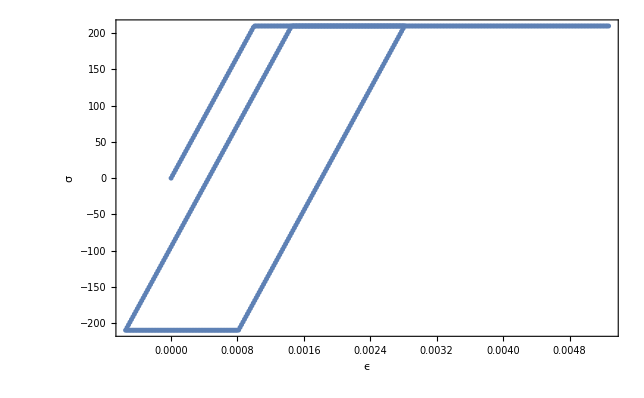

```mathematica
solps=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsig=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
ListPlot[Table[Tooltip[{solps[[i]],solsig[[i]]}],{i,1,Length[solps]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵ","σ"}]
```

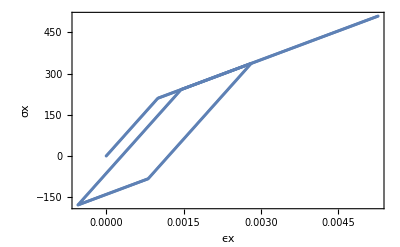

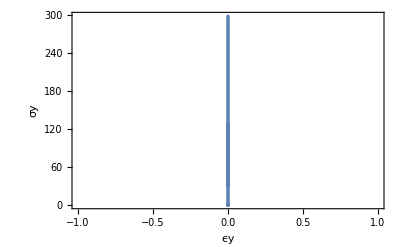

```mathematica
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
ListPlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solps]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"}]
solpsy=Table[epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,2,2]],{i,1,Length[sigvec]}];
ListPlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solps]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵy","σy"}]
```

```mathematica
epsvec[[500]]
```

{{0.00210478,0,0},{0,0,0},{0,0,0}}

```mathematica
sigvec[[500]]
```

{{287.335,0.,0.},{0.,77.3347,0.},{0.,0.,77.3347}}

```mathematica
deps={0.0000353745,0,0}/2;
epst={0,0,0};
epsp={0,0,0};
young=210000;
nu=0.;
De=({{((1-nu) young)/((1-2 nu) (1+nu)), (nu young)/((1-2 nu) (1+nu)), 0}, {(nu young)/((1-2 nu) (1+nu)), ((1-nu) young)/((1-2 nu) (1+nu)), 0}, {0, 0, young/(2 (1+nu))}});
sigy=210;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<680,i++,

{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard];
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[i==160 || i==350,
deps*=-1;
];
epst+=deps;
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. √6 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

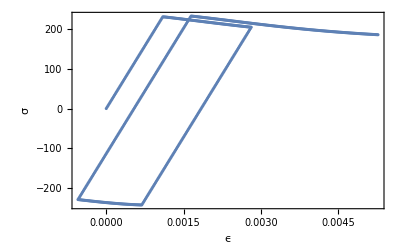

```mathematica
solps=Table[epsvec[[i,1]]-epsvec[[i,2]],{i,1,Length[epsvec]}];
solsig=Table[sigvec[[i,1]]-sigvec[[i,2]],{i,1,Length[sigvec]}];
ListPlot[Table[{solps[[i]],solsig[[i]]},{i,1,Length[solps]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵ","σ"}]
```

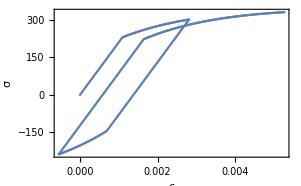

```mathematica
solps=Table[epsvec[[i,1]],{i,1,Length[epsvec]}];
solsig=Table[sigvec[[i,1]],{i,1,Length[sigvec]}];
ListPlot[Table[Tooltip[{solps[[i]],solsig[[i]]}],{i,1,Length[solps]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵ","σ"}]
```

```mathematica
(*Método de verificação do cálculo da derivada, conforme descrição acima*)
checkconv[epst_,epsp_,sigy_,young_,nu_,hard_]:=Block[{nsz=5,sol,incval,numrows,range,i,estimateresidual,res,diffnorm,k,actualstate,tan,referenceresidual,pts,j,incvalres,resstate,eps,stress,Dep,H=hard,Nn},

diffnorm=Table[0,{nsz}];{eps,stress,H,Dep,Nn}=ApplyStrainComputeStress3D[epst,epsp,young,nu,H];
referenceresidual=stress;
tan=Dep;
numrows=Length[eps];
range=Table[0,{numrows}];
incval=Table[0,{numrows}];
range={eps[[1,1]],eps[[2,2]],eps[[1,2]]}/2000;
For[i=1,i<=numrows,i++,
incval[[i]]= range[[i]] RandomReal[];
];

estimateresidual=tan .incval;

For[i=1,i<nsz,i++,
actualstate=({eps[[1,1]],eps[[2,2]],eps[[1,2]]} );

For[k=1,k<=Length[eps],k++,
actualstate[[k]]+=incval[[k]]*(i/nsz);
];
stress3d={{actualstate[[1]],actualstate[[3]],0},{actualstate[[3]],actualstate[[2]],0},{0,0,0}};
{eps,stress,H,Dep,Nn}=ApplyStrainComputeStress3D[stress3d,epsp,young,nu,H];
res={stress[[1,1]],stress[[2,2]],stress[[1,2]]};
res-=referenceresidual;
res=res-estimateresidual(i/nsz);
diffnorm[[i]]=Norm[res];
];
For[i=2,i<nsz,i++,
sol=( Log[10., diffnorm[[i]] ]- Log[10.,diffnorm[[i-1]] ] )/( Log[10.,i]-Log[10.,i-1]);
Print[sol];
];
diffnorm
]
```

```mathematica
epst
epsp
```

{0.00528849,0,0}

{0.00369615,-0.000692872,0.}

```mathematica
De
```

{{210000.,0.,0},{0.,210000.,0},{0,0,105000.}}

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}};
epst={{0,0,0},{0,0,0},{0,0,0}}/2;
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
oldeps=epst;
olstress=epsp;
young=210000;
nu=0.;
De=({{((1-nu) young)/((1-2 nu) (1+nu)), (nu young)/((1-2 nu) (1+nu)), 0}, {(nu young)/((1-2 nu) (1+nu)), ((1-nu) young)/((1-2 nu) (1+nu)), 0}, {0, 0, young/(2 (1+nu))}});

sigy=210;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<140,i++,
olstress=stress;

{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress3D[epst,epsp,young,nu,hard];
checkconv[epst,epsp,sigy,young,nu,hard];
diff=Simplify[De-Dep];
epsp=epst-eps;

Print["Dep = ",MatrixForm[Dep]];
(*Print["stress = ",stress];
Print["De.epst = ",De.epst ];
Print["eps = ",eps];
Print["ept = ",epst];
Print["epsp = ",epsp];
Print["Dep = ",MatrixForm[Dep]];*)
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[i==40 || i==80,
deps*=-1;
];
oldeps=epst;
epst+=deps;
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Indeterminate

Indeterminate

Indeterminate

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000125637

0.000429527

0.000907978

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000128162

0.00043816

0.000926225

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000040577

0.000138731

0.000293285

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.00011826

0.000404309

0.000854674

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000091978

0.00031446

0.000664756

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000226893

0.0000775743

0.000163999

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000121445

0.000415198

0.000877691

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000499613

0.000170814

0.000361109

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000077684

0.000265593

0.00056146

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000074933

0.000256188

0.000541579

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000106341

0.000363562

0.000768548

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000941962

0.000322043

0.000680786

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000809951

0.000276912

0.000585388

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000724433

0.000247676

0.000523587

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000126617

0.000432879

0.000915064

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

3.00109×10^-6

0.0000102608

0.0000216926

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000880073

0.000300885

0.000636062

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000129761

0.000443626

0.000937778

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000111025

0.000379577

0.000802398

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000691923

0.000236561

0.000500092

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000888663

0.000303822

0.00064227

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

9.76675×10^-6

0.0000333926

0.0000705957

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000238533

0.0000815541

0.000172413

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000141609

0.000484128

0.00102338

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000137272

0.000469302

0.000992049

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0000323357

0.000110555

0.000233721

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000116667

0.000398862

0.000843162

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.000102072

0.000348969

0.000737701

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.000655038

-0.00152174

0.000942585

Dep = (3167.08 | 103416. | 0.
103416. | 155663. | 0.
0. | 0. | 102371.)

-0.0241925

-0.041458

-0.0585396

Dep = (3817.16 | 103091. | 0.
103091. | 154850. | 0.
0. | 0. | 101396.)

-0.057076

-0.0977655

-0.137544

Dep = (3805.94 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.0892413

-0.152359

-0.212223

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.120083

-0.202893

-0.276635

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.149991

-0.249801

-0.330058

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.178099

-0.29043

-0.365404

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.205055

-0.325842

-0.373669

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.230185

-0.353606

-0.287795

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.253655

-0.371779

0.096326

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.275454

-0.371033

0.61229

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.305532

-0.211245

1.11608

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.313159

-0.108066

1.16805

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.320883

0.0153246

1.19757

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.328706

0.152712

1.21448

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.336704

0.301534

1.22477

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.344534

0.458578

1.23037

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.351724

0.622131

1.23249

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.357464

0.792047

1.23315

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.357599

0.960455

1.23201

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.332863

1.09489

1.22945

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.254883

1.14749

1.22577

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.149263

1.16228

1.22072

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.0320429

1.16743

1.21445

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0940183

1.16908

1.20749

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.228403

1.16832

1.19931

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.371376

1.16581

1.19021

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.523042

1.16149

1.17991

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.682637

1.15578

1.1614

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.842013

1.14858

1.05398

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.947406

1.13971

0.945913

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.976002

1.1292

0.836983

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.985933

1.11714

0.730781

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.990019

1.10354

0.621345

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.990207

1.0884

0.51193

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.986843

1.07193

0.402373

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.979852

1.05417

0.293002

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.969117

1.0353

0.18413

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.954565

1.01536

0.0762725

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.936312

0.92566

0.0636061

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.914618

0.825085

0.0665699

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.889957

0.72493

0.0688808

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.862839

0.628564

0.0669224

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.833943

0.531219

0.063598

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.803885

0.43563

0.062483

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.773301

0.341895

0.0605918

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.742753

0.250205

0.0579605

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.712621

0.161126

0.0546607

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.681376

0.0772254

0.0515945

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.601606

0.0770889

0.051575

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.524911

0.0762267

0.0513399

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.601604

0.0770947

0.0515866

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.681423

0.0772599

0.0516362

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.712606

0.161211

0.0546852

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.742746

0.250243

0.0579679

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.773303

0.341876

0.0605822

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.803882

0.43563

0.062469

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.833943

0.531224

0.0636061

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.86284

0.628556

0.0669164

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.889947

0.724988

0.0689125

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.91463

0.825019

0.0665364

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.936302

0.925707

0.0636129

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.954564

1.01536

0.0762952

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.969113

1.03528

0.184159

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.979886

1.05424

0.292662

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.986836

1.07191

0.40244

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.990253

1.08849

0.511478

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.990013

1.10351

0.62142

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.985931

1.11714

0.73079

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.975958

1.12912

0.837415

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.947379

1.13964

0.946208

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.842012

1.14859

1.05398

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.682641

1.15578

1.16139

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.523148

1.16172

1.18023

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.371391

1.16582

1.19022

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.228405

1.16834

1.19934

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

0.0940171

1.16908

1.20748

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.0319854

1.16757

1.21466

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.149248

1.16231

1.22078

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.254904

1.14744

1.22571

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.332867

1.09485

1.22942

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.357613

0.960699

1.2322

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.357504

0.792393

1.23339

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.351809

0.622764

1.23292

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.344446

0.45801

1.22999

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.336685

0.301337

1.22463

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.328722

0.152754

1.21448

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.320866

0.0151757

1.19745

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.313181

-0.107903

1.1682

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.305529

-0.211269

1.11603

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.298351

-0.28477

1.03324

Dep = (210000. | 0. | 0
0. | 210000. | 0
0 | 0 | 105000.)

-0.295614

-0.301942

1.01983

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.313664

-0.0826225

1.1719

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.330126

0.194851

1.20925

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.344362

0.463716

1.22056

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.35567

0.712794

1.22333

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.360715

0.938586

1.06475

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.334598

1.09749

0.813862

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.249076

1.14094

0.576801

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.151017

1.15181

0.353216

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

-0.0559564

1.15592

0.143542

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.0356865

1.08031

0.0544965

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.12224

0.948545

0.0555158

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.204458

0.821443

0.0559261

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.28308

0.699254

0.0590069

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.357132

0.582982

0.062235

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.427603

0.471589

0.0656636

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.494874

0.364613

0.0692573

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.558677

0.262226

0.0728492

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)

0.618912

0.164213

0.0762547

Dep = (3805.97 | 103097. | 0.
103097. | 154864. | 0.
0. | 0. | 101413.)